```mathematica
f[x_] = 2 + 0.5 Sin[2 Pi x];
y[w0_, w1_, z_] = w0 + w1 * z;
```

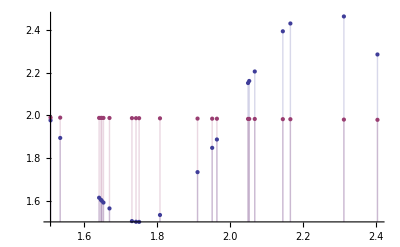

```mathematica
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y[w0, w1, z], {w0, w1}, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y[ws[[1]], ws[[2]], x]}, {x, xVal}]
```